# DM DM -> νν

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

## Load the model, choose the topology and the diagram

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/T12BEWSB.mod

> 61 particles (incl. antiparticles) in 22 classes

> $CounterTerms are ON

> 133 vertices

classes model {T12BEWSB} initialized

Excluding 0 Generic, 4 Classes, and 4 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 4 Classes, and 4 Particles fields

in total: 2 Particles insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

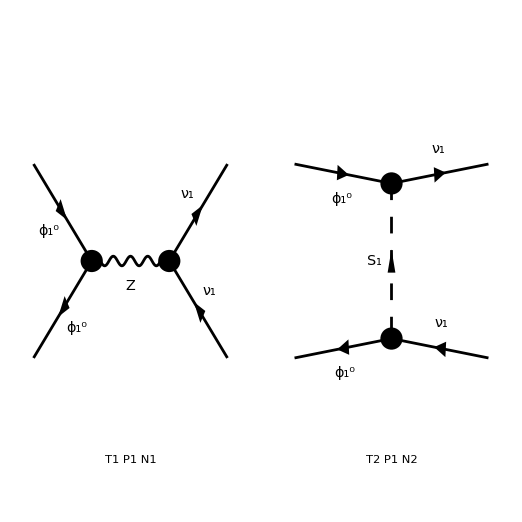

FeynArtsGraphics[{ComposedChar[\phi,1,0],ComposedChar[\phi,1,0]}→{ComposedChar[\nu,1],ComposedChar[\nu,1]}][([T1 P1 N1] | [T2 P1 N2]
Null | Null)]

```mathematica
ClearProcess[];
n22=CreateTopologies[0,2->2]

d22=InsertFields[n22,{F[56,{1}],-F[56,{1}]}->{F[1,{1}],-F[1,{1}]}, InsertionLevel->{Particles},Model->"T12BEWSB",GenericModel->"Lorentz",ExcludeParticles->{S[53],S[54]} ];
Paint[d22,ColumnsXRows->{2,2}]
```

## Amplitude

```mathematica
amp=CreateFeynAmp[d22];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
resultamp = CalcFeynAmp[amp,FermionChains->VA,FermionOrder->None,  Invariants->True];
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-1.frm

running FORM...

ok

#### Rotation matrices: pure singlet limit

```mathematica
Den[x_,y_]:=1/(x-y)
expr0=Simplify[ComplexExpand[Plus@@resultamp//.Subexpr[]//.Abbr[]]/.Alfa->e^2/(4Pi)/.{MasssO1->ms1,MassVZ->MZ,MassFv[1]->mv,MassFn[1]->mx1}/.{RL[1,1]->1,RL[1,2]->0,RL[1,3]->0,RR[1,1]->1,RR[1,2]->0,RR[1,3]->0}]
```

((Mat[(<v2|1|v4>) (<u3|1|u1>)]+Mat[(<v2|5|v4>) (<u3|1|u1>)]-Mat[(<v2|1|v4>) (<u3|5|u1>)]-Mat[(<v2|5|v4>) (<u3|5|u1>)]) SumOver[Ind1,3] SumOver[Ind2,3] XR[1,Ind1] XR[1,Ind2] YfR1[Ind1] YfR1[Ind2])/(4 (ms1^2-T))

```mathematica
InputForm[expr0]
```

((Mat[DiracChain[Spinor[k[2], mx1, -1], 1, Spinor[k[4], mv, -1]]*DiracChain[Spinor[k[3], mv, 1], 1, Spinor[k[1], mx1, 1]]] + 
   Mat[DiracChain[Spinor[k[2], mx1, -1], 5, Spinor[k[4], mv, -1]]*DiracChain[Spinor[k[3], mv, 1], 1, Spinor[k[1], mx1, 1]]] - 
   Mat[DiracChain[Spinor[k[2], mx1, -1], 1, Spinor[k[4], mv, -1]]*DiracChain[Spinor[k[3], mv, 1], 5, Spinor[k[1], mx1, 1]]] - 
   Mat[DiracChain[Spinor[k[2], mx1, -1], 5, Spinor[k[4], mv, -1]]*DiracChain[Spinor[k[3], mv, 1], 5, Spinor[k[1], mx1, 1]]])*SumOver[Ind1, 3]*SumOver[Ind2, 3]*XR[1, Ind1]*XR[1, Ind2]*YfR1[Ind1]*YfR1[Ind2])/(4*(ms1^2 - T))

```mathematica
expr1=expr0/.(SumOver[Ind1,3]*SumOver[Ind2,3]*XR[1,Ind1]*XR[1,Ind2]*YfR1[Ind1]*YfR1[Ind2])->1
```

(Mat[(<v2|1|v4>) (<u3|1|u1>)]+Mat[(<v2|5|v4>) (<u3|1|u1>)]-Mat[(<v2|1|v4>) (<u3|5|u1>)]-Mat[(<v2|5|v4>) (<u3|5|u1>)])/(4 (ms1^2-T))

```mathematica
expr1
```

(Mat[(<v2|1|v4>) (<u3|1|u1>)]+Mat[(<v2|5|v4>) (<u3|1|u1>)]-Mat[(<v2|1|v4>) (<u3|5|u1>)]-Mat[(<v2|5|v4>) (<u3|5|u1>)])/(4 (ms1^2-T))

#### Kind of Dirac Chains in the AMPLITUDE

```mathematica
InputForm[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],1,Spinor[k[1],mx1,1]]]->0,Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],1,Spinor[k[1],mx1,1]]]->0,Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],5,Spinor[k[1],mx1,1]]]->0,Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],5,Spinor[k[1],mx1,1]]]->0}]
```

0

```mathematica
expr2 = Simplify[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],1,Spinor[k[1],mx1,1]]]->F11,Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],1,Spinor[k[1],mx1,1]]]->F51,Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],5,Spinor[k[1],mx1,1]]]->F15,Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],5,Spinor[k[1],mx1,1]]]->F55}]
```

(F11-F15+F51-F55)/(4 ms1^2-4 T)

## Momenta in the computation for the CM frame

```mathematica
kinematic=Solve[{E1==Sqrt[p1^2+mx1^2]&&E2==Sqrt[p2^2+mv^2]&& E2==E1},{E1,E2,p2}][[1]]
```

{E1→√(mx1^2+p1^2),E2→√(mx1^2+p1^2),p2→-√(-mv^2+mx1^2+p1^2)}

In two dimensions...

```mathematica
k1={E1,p1,0,0};
k2={E1,-p1,0,0};
k3={E2,p2*ct,p2*st,0}/.st->Sqrt[1-ct^2];
k4={E2,-p2*ct,-p2*st,0}/.st->Sqrt[1-ct^2];
```

#### Mandelstan variables

```mathematica
guv = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
MatrixForm[guv]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   
		         T->(k1 - k3).guv.(k1 - k3),   
                            U ->(k1 - k4).guv.(k1 - k4)}/.kinematic]
```

{S→4 (mx1^2+p1^2),T→mv^2-mx1^2-2 p1 (p1+ct √(-mv^2+mx1^2+p1^2)),U→mv^2-mx1^2-2 p1 (p1-ct √(-mv^2+mx1^2+p1^2))}

## Dirac spinors and Gamma matrices

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};

gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3};
```

```mathematica
Grid[{{"γ0","γ1","γ2","γ3","γ5"},{gamma0//MatrixForm,gamma1//MatrixForm,gamma2//MatrixForm,gamma3//MatrixForm,gamma5//MatrixForm}},Frame->All]
```

γ0 | γ1 | γ2 | γ3 | γ5
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Check properties of gamma matrices ...

[γu,γv]=2guv

```mathematica
Grid[{{"i=0","i=1","i=2","i=3"},{ Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma0}},{j,{gamma0}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma1}},{j,{gamma1}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma2}},{j,{gamma2}}]] //MatrixForm ,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma3}},{j,{gamma3}}]]//MatrixForm} },Frame->All]
```

i=0 | i=1 | i=2 | i=3
(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
```

χ1 | χ2
(1
0) | (0
1)

Spinors (Cheng appendix)

```mathematica
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+mx1));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+mx1));
σp3=((Total[k3[[#+1]] PauliMatrix[#]&/@Range[3]])/(k3[[1]]+mv));
σp4=((Total[k4[[#+1]] PauliMatrix[#]&/@Range[3]])/(k4[[1]]+mv));
```

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp2,mx1,k2[[1]]]
```

{√(E1+mx1),0,0,-p1/(√(E1+mx1))}

```mathematica
vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp2,mx1,k2[[1]]]
```

{0,-p1/(√(E1+mx1)),√(E1+mx1),0}

Check normalization for the U Spinors (input and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.uspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,mx1,k2[[1]]]]).gamma0.uspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.uspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[uspinor[1,σp4,mx1,k4[[1]]]]).gamma0.uspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

2 mx1

Check normalization for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.vspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Me,k2[[1]]]]).gamma0.vspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[vspinor[1,σp3,mx1,k3[[1]]]]).gamma0.vspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[vspinor[1,σp4,mx1,k4[[1]]]]).gamma0.vspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

-2 mx1

(OverBar[U1]γaU2)^†=(OverBar[U2]γaU1)

```mathematica
AA1=(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.uspinor[1,σp3,mx1,k3[[1]]];
AA2=(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.gamma2.uspinor[1,σp1,mx1,k1[[1]]];
Simplify[Conjugate[AA1]-AA2]
```

0

```mathematica
BB1=Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.vspinor[1,σp4,mx1,k3[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]];
BB2=Simplify[(Conjugate[vspinor[1,σp4,mx1,k3[[1]]]]).gamma0.gamma2.vspinor[1,σp1,mx1,k1[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]];
Simplify[Simplify[(Conjugate[BB1]-BB2),Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]]
```

0

## Amplitude square

Manipulation of the amplitude

#### Dirac Chains in the amplitude (F11,F15,F51,F55)

```mathematica
Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],1,Spinor[k[1],mx1,1]]]->F11,Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],1,Spinor[k[1],mx1,1]]]->F51,Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],5,Spinor[k[1],mx1,1]]]->F15,Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[4],mv,-1]]*DiracChain[Spinor[k[3],mv,1],5,Spinor[k[1],mx1,1]]]->F55
```

```mathematica
expr1
```

(Mat[(<v2|1|v4>) (<u3|1|u1>)]+Mat[(<v2|5|v4>) (<u3|1|u1>)]-Mat[(<v2|1|v4>) (<u3|5|u1>)]-Mat[(<v2|5|v4>) (<u3|5|u1>)])/(4 (ms1^2-T))

```mathematica
Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]
```

Mat[<v2|1|u1>]

Mat[<v2|5|u1>]

Mat[<v2|1,k[3]|u1>]

Mat[<v2|5,k[3]|u1>]

#### FULL Amplitude

```mathematica
AMP[s1_,s2_,s3_,s4_]:=expr2/.{
F11->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,IdentityMatrix[4]],vspinor[s4,σp4,mv,k4[[4]]]]*Dot[(Conjugate[uspinor[s3,σp3,mv,k3[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[4]]]],
F15->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],vspinor[s4,σp4,mv,k4[[4]]]]*Dot[(Conjugate[uspinor[s3,σp3,mv,k3[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[4]]]],
F51->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],vspinor[s4,σp4,mv,k4[[4]]]]*Dot[(Conjugate[uspinor[s3,σp3,mv,k3[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[4]]]],
F55->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],vspinor[s4,σp4,mv,k4[[4]]]]*Dot[(Conjugate[uspinor[s3,σp3,mv,k3[[1]]]]).Dot[gamma0,gamma5],uspinor[s1,σp1,mx1,k1[[4]]]]
}
```

```mathematica
AMP[1,1,-1,-1]
```

-((-(√mv (-ct p2+ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(E2+mv)-√mv (1/(√(E1+mx1)))^* p1^*) ((√mx1 p1 (√(E2+mv))^*)/(E1+mx1)-√mx1 (1/(√(E2+mv)))^* (ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*)))/(4 ms1^2-4 T)

Sum over spinors and gamma matrices.. trick! Warning: I do the gamma matrices explicitly because i need to avoid the index in the gamma_uv.

#### FULL Amplitude squared

```mathematica
AMP2=(1/4)*(1/2)*(Sum[AMP[s1,s2,s3,s4]*Conjugate[AMP[s1,s2,s3,s4]],{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}},{s4,{-1,1}}])/.{st->Sqrt[1-ct^2]}
```

1/8 (((-((ct p2+ⅈ √(1-ct^2) p2) (√mx1)^*)/(√(E2+mv))+(√(E2+mv) (√mx1)^* p1^*)/(E1^*+mx1^*)) (-(√mv (-ct p2+ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(E2+mv)-√mv (1/(√(E1+mx1)))^* p1^*) (-(p1 (√mv)^*)/(√(E1+mx1))-(√(E1+mx1) (√mv)^* (-ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*))/(E2^*+mv^*)) ((√mx1 p1 (√(E2+mv))^*)/(E1+mx1)-√mx1 (1/(√(E2+mv)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((√(E2+mv) (√mx1)^*-((ct p2+ⅈ √(1-ct^2) p2) (√mx1)^* p1^*)/(√(E2+mv) (E1^*+mx1^*))) (-√mv (√(E1+mx1))^*-(√mv (-ct p2+ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*)/(E2+mv)) (-√(E1+mx1) (√mv)^*-(p1 (√mv)^* (-ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*))/(√(E1+mx1) (E2^*+mv^*))) (√mx1 (√(E2+mv))^*-(√mx1 p1 (1/(√(E2+mv)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*))/(E1+mx1)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((-((ct p2+ⅈ √(1-ct^2) p2) (√mx1)^*)/(√(E2+mv))+(√(E2+mv) (√mx1)^* p1^*)/(E1^*+mx1^*)) (-(√mv (-ct p2-ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(E2+mv)-√mv (1/(√(E1+mx1)))^* p1^*) ((√mx1 p1 (√(E2+mv))^*)/(E1+mx1)-√mx1 (1/(√(E2+mv)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*)) (-(p1 (√mv)^*)/(√(E1+mx1))-(√(E1+mx1) (√mv)^* (-ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*))/(E2^*+mv^*)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((√(E2+mv) (√mx1)^*-((ct p2+ⅈ √(1-ct^2) p2) (√mx1)^* p1^*)/(√(E2+mv) (E1^*+mx1^*))) (-√mv (√(E1+mx1))^*-(√mv (-ct p2-ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*)/(E2+mv)) (√mx1 (√(E2+mv))^*-(√mx1 p1 (1/(√(E2+mv)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*))/(E1+mx1)) (-√(E1+mx1) (√mv)^*-(p1 (√mv)^* (-ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*))/(√(E1+mx1) (E2^*+mv^*))))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((-((ct p2-ⅈ √(1-ct^2) p2) (√mx1)^*)/(√(E2+mv))+(√(E2+mv) (√mx1)^* p1^*)/(E1^*+mx1^*)) (-(√mv (-ct p2+ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(E2+mv)-√mv (1/(√(E1+mx1)))^* p1^*) (-(p1 (√mv)^*)/(√(E1+mx1))-(√(E1+mx1) (√mv)^* (-ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*))/(E2^*+mv^*)) ((√mx1 p1 (√(E2+mv))^*)/(E1+mx1)-√mx1 (1/(√(E2+mv)))^* (ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((-((ct p2-ⅈ √(1-ct^2) p2) (√mx1)^*)/(√(E2+mv))+(√(E2+mv) (√mx1)^* p1^*)/(E1^*+mx1^*)) (-(√mv (-ct p2-ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(E2+mv)-√mv (1/(√(E1+mx1)))^* p1^*) (-(p1 (√mv)^*)/(√(E1+mx1))-(√(E1+mx1) (√mv)^* (-ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*))/(E2^*+mv^*)) ((√mx1 p1 (√(E2+mv))^*)/(E1+mx1)-√mx1 (1/(√(E2+mv)))^* (ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((√(E2+mv) (√mx1)^*-((ct p2-ⅈ √(1-ct^2) p2) (√mx1)^* p1^*)/(√(E2+mv) (E1^*+mx1^*))) (-√mv (√(E1+mx1))^*-(√mv (-ct p2+ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*)/(E2+mv)) (-√(E1+mx1) (√mv)^*-(p1 (√mv)^* (-ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*))/(√(E1+mx1) (E2^*+mv^*))) (√mx1 (√(E2+mv))^*-(√mx1 p1 (1/(√(E2+mv)))^* (ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*))/(E1+mx1)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2))+((√(E2+mv) (√mx1)^*-((ct p2-ⅈ √(1-ct^2) p2) (√mx1)^* p1^*)/(√(E2+mv) (E1^*+mx1^*))) (-√mv (√(E1+mx1))^*-(√mv (-ct p2-ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*)/(E2+mv)) (-√(E1+mx1) (√mv)^*-(p1 (√mv)^* (-ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*))/(√(E1+mx1) (E2^*+mv^*))) (√mx1 (√(E2+mv))^*-(√mx1 p1 (1/(√(E2+mv)))^* (ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*))/(E1+mx1)))/((4 ms1^2-4 T) (-4 T+4 (ms1^*)^2)))

```mathematica
kk=FullSimplify[AMP2,Element[{ct,mx1,mv,√mv,√mx1,E1,E2,ms1,p1,p2,√(E1+mx1),√(E2+mv),1/(√(E2+mv)),1/(√(E1+mx1)),√(1-ct^2)}, Reals]]
```

(mv mx1 (((E2+mv) (E1+mx1)-(ct+ⅈ √(1-ct^2)) p1 p2)^2 ((E2+mv) (E1+mx1)+ⅈ (ⅈ ct+√(1-ct^2)) p1 p2)^2+((E2+mv)^2 p1^2-2 ct (E2+mv) (E1+mx1) p1 p2+(E1+mx1)^2 p2^2)^2))/(32 (E2+mv)^3 (E1+mx1)^3 (ms1^2-T)^2)

## Differential cross section approximation

```mathematica
expr4=kk/.kinematic/.MV
```

(mv mx1 (((ct+ⅈ √(1-ct^2)) p1 √(-mv^2+mx1^2+p1^2)+(mv+√(mx1^2+p1^2)) (mx1+√(mx1^2+p1^2)))^2 (-ⅈ (ⅈ ct+√(1-ct^2)) p1 √(-mv^2+mx1^2+p1^2)+(mv+√(mx1^2+p1^2)) (mx1+√(mx1^2+p1^2)))^2+(p1^2 (mv+√(mx1^2+p1^2))^2+2 ct p1 √(-mv^2+mx1^2+p1^2) (mv+√(mx1^2+p1^2)) (mx1+√(mx1^2+p1^2))+(-mv^2+mx1^2+p1^2) (mx1+√(mx1^2+p1^2))^2)^2))/(32 (mv+√(mx1^2+p1^2))^3 (mx1+√(mx1^2+p1^2))^3 (ms1^2-mv^2+mx1^2+2 p1 (p1+ct √(-mv^2+mx1^2+p1^2)))^2)

```mathematica
Limit[expr4,mv->0]
```

0

```mathematica
expr5=Simplify[expr4/.p1->mx1*v]
```

(mv mx1 (((ct-ⅈ √(1-ct^2)) mx1 v √(-mv^2+mx1^2 (1+v^2))+(mv+√(mx1^2 (1+v^2))) (mx1+√(mx1^2 (1+v^2))))^2 ((ct+ⅈ √(1-ct^2)) mx1 v √(-mv^2+mx1^2 (1+v^2))+(mv+√(mx1^2 (1+v^2))) (mx1+√(mx1^2 (1+v^2))))^2+(mx1^2 v^2 (mv+√(mx1^2 (1+v^2)))^2+2 ct mx1 v √(-mv^2+mx1^2 (1+v^2)) (mv+√(mx1^2 (1+v^2))) (mx1+√(mx1^2 (1+v^2)))+(-mv^2+mx1^2 (1+v^2)) (mx1+√(mx1^2 (1+v^2)))^2)^2))/(32 (mv+√(mx1^2 (1+v^2)))^3 (mx1+√(mx1^2 (1+v^2)))^3 (ms1^2-mv^2+mx1^2+2 mx1 v (mx1 v+ct √(-mv^2+mx1^2 (1+v^2))))^2)

Diferential cross section: General expression (7.106 LAHIRI PAL book)
dσ/dΩ=1/(64 π^2 s)√[({s-(m1'+m2')^2}{s-(m1'-m2')^2})/({s-(m1+m2)^2}{s-(m1-m2)^2})]OverBar[|M|^2]

```mathematica
dcs=(1/(64 π^2 S)*((S-(mv+mv)^2)/(S-(mx1+mx1)^2))^(1/2)*expr5)/.MV/.p1->mx1*v;
```

Multiply by the relative velocity (vr=2v) and expand

```mathematica
vdcs=(2*v)*dcs;
```

```mathematica
expr6= Simplify[Normal[Series[vdcs,{v,0,1}]],mx1>0]
```

(mv √(1-mv^2/mx1^2) (-mv^4-6 ct mv^2 mx1 √(-mv^2+mx1^2) v+mx1^3 (mx1-2 ct √(-mv^2+mx1^2) v)+ms1^2 (mv^2+mx1 (mx1+2 ct √(-mv^2+mx1^2) v))))/(1024 (mv+mx1) (ms1^2-mv^2+mx1^2)^3 π^2)

s - wave

```mathematica
expr6/.v->0
```

(mv √(1-mv^2/mx1^2) (-mv^4+mx1^4+ms1^2 (mv^2+mx1^2)))/(1024 (mv+mx1) (ms1^2-mv^2+mx1^2)^3 π^2)

p - wave

```mathematica
Simplify[D[expr6,v]]/.v->0
```

-(ct mv √(1-mv^2/mx1^2) mx1 √(-mv^2+mx1^2) (-ms1^2+3 mv^2+mx1^2))/(512 (mv+mx1) (ms1^2-mv^2+mx1^2)^3 π^2)

## Cross section

```mathematica
σv=(-∫_1^-1 (expr6)*(2π)ⅆct)
```

(mv √(1-mv^2/mx1^2) (mv^2+mx1^2))/(256 (mv+mx1) (ms1^2-mv^2+mx1^2)^2 π)

```mathematica
σvr=Simplify[σv/.{v->vr/2}]
```

(mv √(1-mv^2/mx1^2) (mv^2+mx1^2))/(256 (mv+mx1) (ms1^2-mv^2+mx1^2)^2 π)

```mathematica
σvr
```

(mv √(1-mv^2/mx1^2) (mv^2+mx1^2))/(256 (mv+mx1) (ms1^2-mv^2+mx1^2)^2 π)

```mathematica
Normal[Series[σvr,{mv,0,1}]]
```

(mv mx1)/(256 (ms1^2+mx1^2)^2 π)